# Classification of Liver Disease in Indian patients Author: Koyel Majumdar(19200368) Date: 3rd December, 2019 Module: Mathematica for Research(ACM40730)-Project

## Introduction

Liver disease is any condition that affects the functioning of liver and causes its inflammation. It can be caused due to injury, exposure to toxic compounds or certain drugs, or due to genetic defects. Around 10 lakh patients are diagnosed every year in India with liver cirrhosis and is among the most common causes of death in India. Statistics show every one in five Indians maybe affected by liver disease.
A doctor may request a blood test for detecting liver disease. A liver panel test contains the below tests:
a) Alanine aminotransferase (ALT) – an enzyme found mainly in the liver; best test to detect hepatitis
b) Alkaline phosphatase (ALP) – an enzyme related to the bile ducts; often increased if ducts are blocked
c) Aspartate aminotransferase (AST) – an enzyme found in the liver and a few other places, particularly the heart and other muscles
d) Total bilirubin – measures the bilirubin in the blood; levels are increased with many liver diseases and other conditions, such as hemolysis, that lead to increased production of bilirubin
e) Direct bilirubin – measures a form of bilirubin that is conjugated (combined with another compound) in the liver; only increased in liver disease
f) Albumin – measures albumin, the main protein made by the liver, and tells how well the liver is making it
g) Total protein – measures albumin and all other proteins in blood, including antibodies present to help fight off infections (antibodies are not made in the liver)

About the dataset

A dataset has been collected from test samples in Andhra Pradesh, India. The dataset contains 416 liver patient records and 167 non liver patient records. There are 441 male patient and 142 female patient records. The dataset has been collected from UCI Machine Learning Repository. The liver dataset contains data of liver panel tests done on these patients and they have been categorized as suffering from liver disease or not. 
Attribute Information:
1) ‘Age’ of the patient
2) ‘Gender’ of the patient
3) ‘Total_Bilirubin’ level
4) ‘Direct_Bilirubin’ level
5) ‘Alkaline_Phosphatase’ level - ALP test
6) ‘Alanine_Aminotransferase’ level - ALT test
7) ‘Aspartate_Aminotransferase’ level - SGOT test
8) ‘Total_Proteins’ level
9) ‘Albumin’ content
10) ‘Albumin_and_Globulin_Ratio’ 
11) ‘Dataset’ classifying a patient having liver disease as ‘1’ and patients not having liver disease as ‘2’

Explanatory Data Analysis will be applied on this dataset to understand the data and the relation between each variable. The analysis will help to understand what are the identifiers of a person having a liver disease. The dataset will be then used to train and test the machine learning algorithms to classify patients into groups having liver disease and the model accuracy will be compared for the different models.

## Data Import

The dataset will be selected from a location in the local server and imported into Mathematica-

```mathematica
filename=SystemDialogInput["FileOpen"];
file=Import[filename,"Dataset","HeaderLines"->1]//Map[Association];
file[1;;3]   (*Displaying the first 3 rows of data *)
```

Dataset[<>]

## Exploratory Data Analysis

Statistical Summary of each column:

The 5-number summary(minimum,lower quantile, median, upper quantile and maximum) along with mean and standard deviation of each predictor variable will calculated. This will help to describe the spread of the data and determine whether or not any data points are outliers. A function has been written to calculate the statistical summary of each numeric variable. A boxplot is plotted to get a visual representation of the statistical summary.

```mathematica
statisticalSummary[x_]:={Clear[mean,sd,min,max,median,quantile25,quantile75],
mean=N[Mean[file[All,x]]],
sd=N[StandardDeviation[file[All,x]]],
min=Min[file[All,x]],
max=Max[file[All,x]],
median=Median[file[All,x]],
quantile25=Quantile[file[All,x],1/4],
quantile75=Quantile[file[All,x],3/4],
Print["Mean=",mean,"\n" ,"Standard Deviation=",sd,"\n","Minimum=",min,
"\n","Maximum=",max,"\n","Median=",median,"\n","1st Quantile=",quantile25,"\n","3rd Quantile=",quantile75]};
```

#### Age-

```mathematica
statisticalSummary["Age"];
```

Mean=44.7461
Standard Deviation=16.1898
Minimum=4
Maximum=90
Median=45
1st Quantile=33
3rd Quantile=58

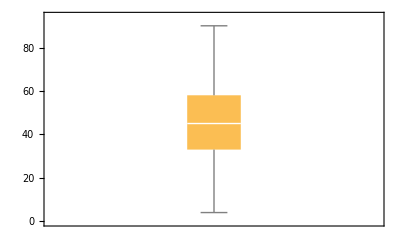

```mathematica
BoxWhiskerChart[file[All,"Age"]]
```

The summary shows that the data has been collected for age range from 4 to 90. The mean and median is almost equal which indicates that the distribution is normal. 25% of data has been collected between age range of 4-33 and 75% of data between 4-58.  No outlier is observed in the boxplot and the median is lying between the 1st and 3rd quantile which reconfirms the normal distribution of the data.

#### Total Bilirubin-

```mathematica
statisticalSummary["Total_Bilirubin"];
```

Mean=3.2988
Standard Deviation=6.20952
Minimum=0.4
Maximum=75
Median=1
1st Quantile=0.8
3rd Quantile=2.6

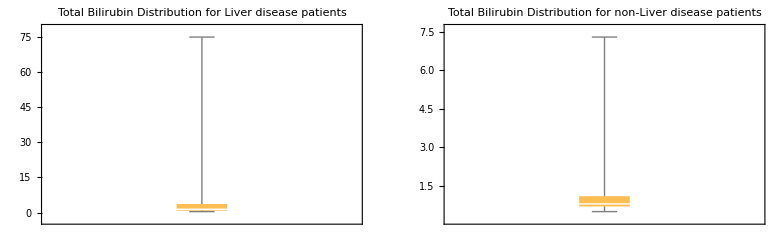

```mathematica
GraphicsRow[
{BoxWhiskerChart[Select[file,#Dataset==1 &][[All,"Total_Bilirubin"]],PlotLabel->"Total Bilirubin Distribution for Liver disease patients",ImageSize->Medium],
BoxWhiskerChart[Select[file,#Dataset==2 &][[All,"Total_Bilirubin"]],PlotLabel->"Total Bilirubin Distribution for non-Liver disease patients"]}]
```

The data collected ranges from 0.4 to 75. Around 25% of people  have total bilirubin level below 0.8 and 50% people have bilirubin level below 2.6. The median is less than the mean which indicates that the distribution is positively skewed. 25% of people are noted to be having total bilirubin level of 2.6-75. The boxplot shows the range is from 0.5-7.3 for patients not having liver disease but the data is varying largely from 0.4 to 75 for patients marked as Liver patients with 25% of the patients having value from 3.7-75. This shows that liver disease cannot be detected only based on this variable.

#### Direct Bilirubin-

```mathematica
statisticalSummary["Direct_Bilirubin"];
```

Mean=1.48611
Standard Deviation=2.8085
Minimum=0.1
Maximum=19.7
Median=0.3
1st Quantile=0.2
3rd Quantile=1.3

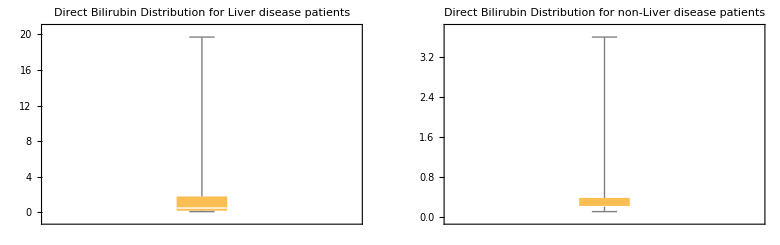

```mathematica
GraphicsRow[
{BoxWhiskerChart[Select[file,#Dataset==1 &][[All,"Direct_Bilirubin"]],
PlotLabel->"Direct Bilirubin Distribution for Liver disease patients",ImageSize->Medium],
BoxWhiskerChart[Select[file,#Dataset==2 &][[All,"Direct_Bilirubin"]],PlotLabel->"Direct Bilirubin Distribution for non-Liver disease patients"]}]
```

The data ranges from 0.1-19.7. The mean is greater than median which indicates the  distribution is positively skewed with 25% of people having level between 1.3-19.7. The range of data is from 0.1-3.6 for non-liver patients but the values vary from 0.1-19.7 for liver patients with 75% of patients having levels below 1.8. So a patient cannot be identified as having liver disease based on only this variable.

#### Alkaline Phosphatase-

```mathematica
statisticalSummary["Alkaline_Phosphatase"];
```

Mean=290.576
Standard Deviation=242.938
Minimum=63
Maximum=2110
Median=208
1st Quantile=175
3rd Quantile=298

Mean=290.576
Standard Deviation=242.938
Minimum=63
Maximum=2110
Median=208
1st Quantile=175
3rd Quantile=298

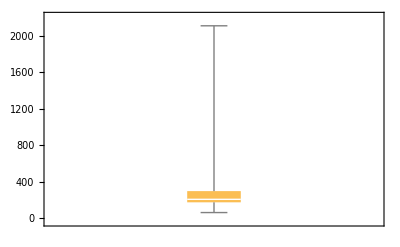

```mathematica
BoxWhiskerChart[file[All,"Alkaline_Phosphatase"]]
```

The data ranges from 63-2110. The mean is greater than median which indicates the  distribution is positively skewed with 25% of people having level between 298-2110. Around 25% of patients are seem to be having very high levels of alkaline phosphatase as indicated in the boxplot.

#### Alanine_Aminotransferase

```mathematica
statisticalSummary["Alanine_Aminotransferase"];
```

Mean=80.7136
Standard Deviation=182.62
Minimum=10
Maximum=2000
Median=35
1st Quantile=23
3rd Quantile=61

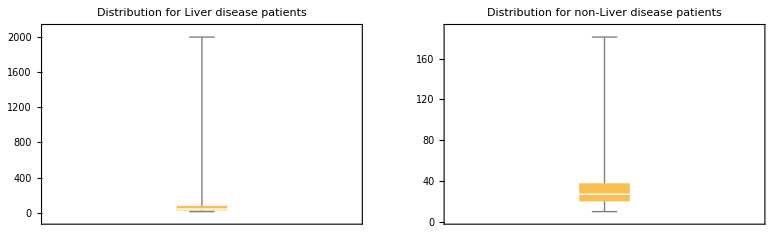

```mathematica
GraphicsRow[
{BoxWhiskerChart[Select[file,#Dataset==1 &][[All,"Alanine_Aminotransferase"]],PlotLabel->"Distribution for Liver disease patients",ImageSize->Medium],
BoxWhiskerChart[Select[file,#Dataset==2 &][[All,"Alanine_Aminotransferase"]],PlotLabel->"Distribution for non-Liver disease patients"]}]
```

The data ranges from 10-2000. The mean is greater than median which indicates the  distribution is positively skewed with 25% of people having level between 61-2000. Again a few cases of very high levels of alanine aminotransferase are indicated. Around 25% of people are observed to be having Alanine aminotransferase level below 23. The non-liver patients seem to be within the range of 10-181 and 25% of patients are having relatively higher values. The liver patients seem to be having very high levels of alanine aminotransferase.

#### Aspartate_Aminotransferase

```mathematica
statisticalSummary["Aspartate_Aminotransferase"];
```

Mean=109.911
Standard Deviation=288.919
Minimum=10
Maximum=4929
Median=42
1st Quantile=25
3rd Quantile=87

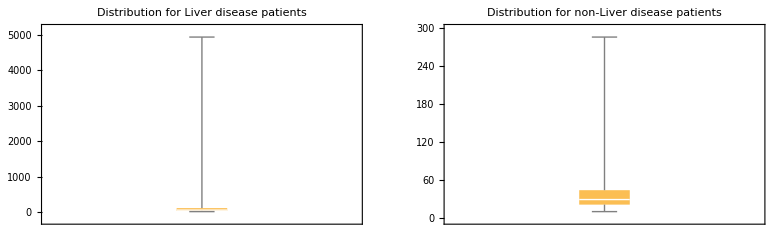

```mathematica
GraphicsRow[
{BoxWhiskerChart[Select[file,#Dataset==1 &][[All,"Aspartate_Aminotransferase"]],PlotLabel->"Distribution for Liver disease patients",ImageSize->Medium],
BoxWhiskerChart[Select[file,#Dataset==2 &][[All,"Aspartate_Aminotransferase"]],PlotLabel->"Distribution for non-Liver disease patients"]}]
```

The data ranges from 10-4929. The mean is greater than median which indicates the  distribution is positively skewed with 25% of people having level above 87. Again a few cases of very high levels of aspartate aminotransferase are indicated. The boxplot shows a liver patients having very high levels of aspartate aminotransferase, whereas the non-liver patients are within the range of 10-285.

#### Total_Proteins-

```mathematica
statisticalSummary["Total_Proteins"];
```

Mean=6.48319
Standard Deviation=1.08545
Minimum=2.7
Maximum=9.6
Median=6.6
1st Quantile=5.8
3rd Quantile=7.2

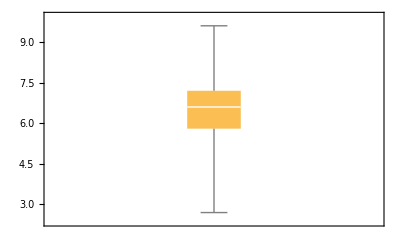

```mathematica
BoxWhiskerChart[file[All,"Total_Proteins"]]
```

The data ranges from 2.7-9.6. The mean is almost equal to median which indicates the  distribution is normal. Around 25% of people are noted to be having level between 7.2-9.6. The boxplot shows almost normal distribution of data.

#### Albumin-

```mathematica
statisticalSummary["Albumin"];
```

Mean=3.14185
Standard Deviation=0.795519
Minimum=0.9
Maximum=5.5
Median=3.1
1st Quantile=2.6
3rd Quantile=3.8

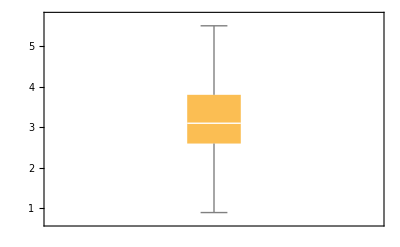

```mathematica
BoxWhiskerChart[file[All,"Albumin"]]
```

The data ranges from 0.9-5.5. The mean is almost equal to median which indicates the  distribution is normal. A total of 25% of data is found to be having level between 3.8-5.5 and no cases of high variation is observed. The boxplot shows the median is a little closer to the 1st quantile and the data is almost normally distributed.

#### Albumin_and _Globulin _Ratio-

```mathematica
statisticalSummary["Albumin_and_Globulin_Ratio"];
```

Mean=0.947063
Standard Deviation=0.318492
Minimum=0.3
Maximum=2.8
Median=0.947
1st Quantile=0.7
3rd Quantile=1.1

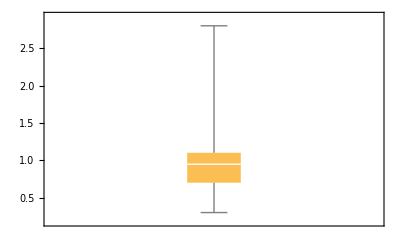

```mathematica
BoxWhiskerChart[file[All,"Albumin_and_Globulin_Ratio"]]
```

The data ranges from 0.3-2.8. The mean is equal to median and hence the data is normally distributed. No cases with high variation in data is observed. The same can be observed from the boxplot.

Data Visualization

## Patients with and without liver disease

A histogram is plotted to have a visual representation of the number of cases with liver disease and non-liver disease cases.

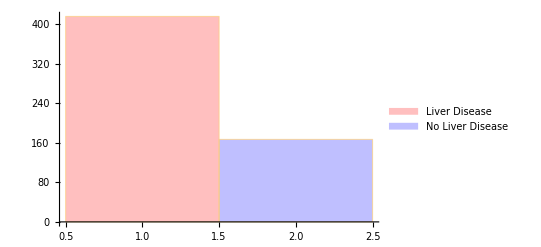

```mathematica
Histogram[file[All,"Dataset"],ChartStyle->{Opacity[.25,Red],Opacity[.25,Blue]},ChartLegends->{"Liver Disease","No Liver Disease"},Axes->{False,True}]
```

## Gender count

The categorical variable “Gender” is converted to indicate 0 as “Males” and 1 as “Females”. A histogram is plotted to represent number of male and female patients reported.

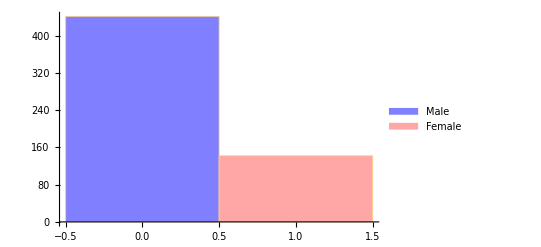

```mathematica
gender[x_]:=If[x=="Male",0,1];
newfile=file[All,{"Gender"->gender}];
Histogram[newfile[All,"Gender"],ChartStyle->{Opacity[.5,Blue],Opacity[.35,Red]},ChartLegends->{"Male","Female"},Axes->{False,True}]
```

The histogram shows that 441 cases are of male patients and 142 cases are reported for female patients.

## Age factor

The number of patients in each gender group classified as a liver patient or not is calculated and their average age is calculated. A histogram is plotted to view the relation of age to the disease.

### Number of Males with Disease and their average Age

The average age of male patients reported as liver patients is 47.

```mathematica
k=Length[Select[newfile,#Gender==0 && #Dataset==1 &][[All,1]]]
N[Total[Select[newfile,#Gender==0 && #Dataset==1 &][[All,1]]]/k]
```

324

46.9506

### Number of Males without Disease and their average Age

The average age of male patients not reported as liver patients is 41.

```mathematica
Clear[k];
k=Length[Select[newfile,#Gender==0 && #Dataset==2&][[All,1]]]
N[Total[Select[newfile,#Gender==0 && #Dataset==2 &][[All,1]]]/k]
```

117

40.5983

### Number of Females with Disease and their average Age

The average age of female patients reported as liver patients is 43.

```mathematica
Clear[k];
k=Length[Select[newfile,#Gender==1 && #Dataset==1 &][[All,1]]]
N[Total[Select[newfile,#Gender==1 && #Dataset==1 &][[All,1]]]/k]
```

92

43.3478

### Number of Females without Disease and their average Age

The average age of female patients not reported as liver patients is 43.

```mathematica
Clear[k];
k=Length[Select[newfile,#Gender==1&& #Dataset==2 &][[All,1]]]
N[Total[Select[newfile,#Gender==1 && #Dataset==2 &][[All,1]]]/k]
```

50

42.74

### Histogram of Age as per Gender and Disease

The histogram is plotted to view which age group has more liver patients reported for each gender.

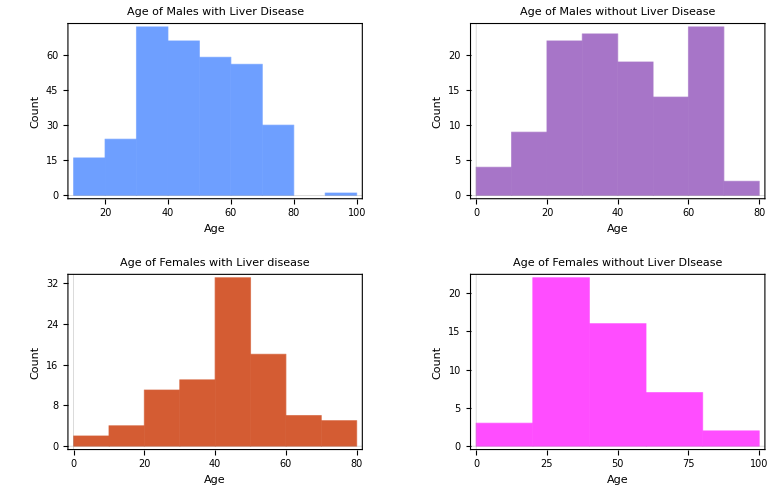

```mathematica
GraphicsGrid[{{Histogram[Select[newfile,#Gender==0 && #Dataset==1 &][[All,1]],Axes->{True,True},Frame->True,FrameLabel->{"Age","Count"},PlotLabel->"Age of Males with Liver Disease",PlotTheme->{"BoldLabels","CoolColor","Scientific" }, ImageSize->Medium],Histogram[Select[newfile,#Gender==0 && #Dataset==2 &][[All,1]],Axes->{True,True},Frame->True,FrameLabel->{"Age","Count"},PlotLabel->"Age of Males without Liver Disease",PlotTheme->{"BoldLabels","RoyalColor","Scientific" }]},{Histogram[Select[newfile,#Gender==1 && #Dataset==1 &][[All,1]],Axes->{True,True},Frame->True,FrameLabel->{"Age","Count"},PlotLabel->"Age of Females with Liver disease",PlotTheme->{"BoldLabels","VibrantColor","Scientific" }],Histogram[Select[newfile,#Gender==1 && #Dataset==2 &][[All,1]],Axes->{True,True},Frame->True,FrameLabel->{"Age","Count"},PlotLabel->"Age of Females without Liver DIsease", PlotTheme->{"BoldLabels","Scientific" },ChartStyle->Hue[5/6,0.7]]}}]
```

### Observations:

The average age suggests the male patients with increasing age has a tendency of being affected by liver disease. The average age for females are not conclusive as both the patient group is calculated to be having same average age. 
The histogram plot is a better representation of age being a factor in the patient being affected. For the male group it can be seen more cases are reported between age group 30-80 and very few cases in this age group is reported to be not having liver disease. In case of female patients 75 of liver disease cases are reported in the age group of 20-60 whereas 38 are reported to be not having liver disease in this age group. So it can be concluded that as age increases the probability of having liver disease increases in both male and female patients.

## Relation between Direct Bilirubin and Total Bilirubin

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Total Bilirubin” and “Direct Bilirubin”.

### Scatter Plot to determine Relationship

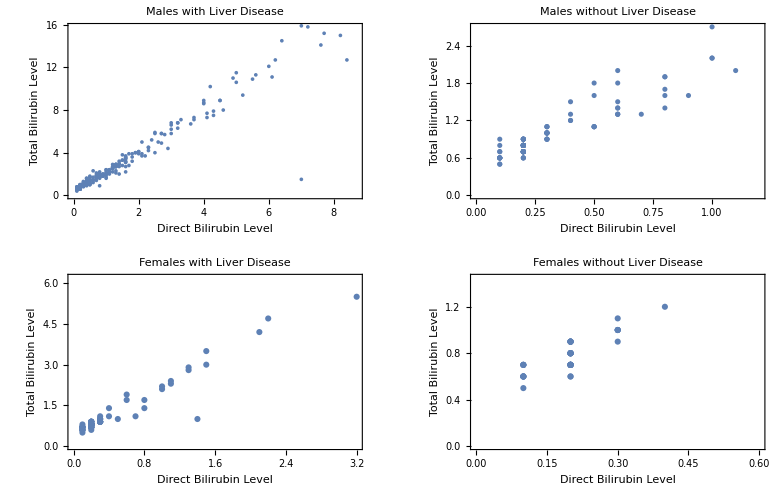

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{4,3}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Direct Bilirubin Level","Total Bilirubin Level"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{4,3}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Direct Bilirubin Level","Total Bilirubin Level"},Frame->True,FrameLabel->{"Direct Bilirubin Level","Total Bilirubin Level"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{4,3}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Direct Bilirubin Level","Total Bilirubin Level"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{4,3}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Direct Bilirubin Level","Total Bilirubin Level"}]}}]
```

### Correlation Test:

```mathematica
Correlation[file[All,"Total_Bilirubin"]//Normal,file[All,"Direct_Bilirubin"]//Normal]
```

0.874618

### Observations:

The variables “Total Bilirubin” and “Direct Bilirubin” is observed to be having a direct linear relationship and the correlation coefficient is also observed to be very high. We could have removed one of the variables from the model due to this direct relation but it should not be removed. Both of them indicates jaundice in the patient but they indicate different types of jaundice. Also an increase in total bilirubin does not always indicate an increase in direct bilirubin. It can also increase due to increase in indirect bilirubin. So we will be keeping both the variables in the model.

## Relation between Aspartate Aminotransferase and Alanine AminoTransferase

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Aspartate Aminotransferase” and “Alanine Aminotransferase”.

### Scatter Plot to determine Relationship

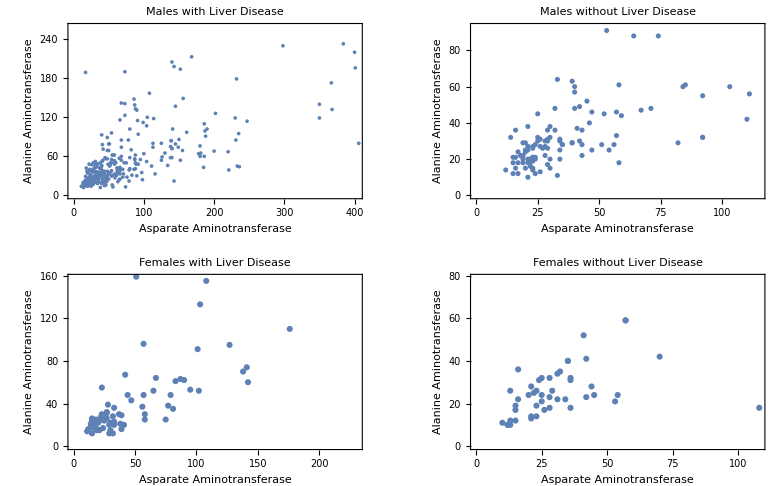

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{7,6}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Asparate Aminotransferase","Alanine Aminotransferase"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{7,6}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Asparate Aminotransferase","Alanine Aminotransferase"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{7,6}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Asparate Aminotransferase","Alanine Aminotransferase"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{7,6}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Asparate Aminotransferase","Alanine Aminotransferase"}]}}]
```

### Correlation Test:

```mathematica
N[Correlation[file[All,"Aspartate_Aminotransferase"]//Normal,file[All,"Alanine_Aminotransferase"]//Normal]]
```

0.791966

### Observations:

A linear relationship is observed between Aspartate Aminotransferase(AST) and Alanine Aminotransferase(ALT) which shows patients with high AST level also has a tendency of high ALT level. A high correlation coefficient  is obtained between them which shows us a possibility that one of the variables can be removed from the model. However, an increase in either of ALT or AST or both does not indicate the degree of liver damage. An increase might reflect a temporary insignificant liver damage as well as severe liver damage with long term consequences. Generally an increase of more than 3 times of normal value of AST and ALT signifies some degree of liver damage either temporary or permanent. Therefore we need to keep both the variables in the model.

## Relation between Alkaline Phosphatase and Alanine AminoTransferase

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Alkaline Phosphatase” and “Alanine Aminotransferase”.

### Scatter Plot to determine Relationship

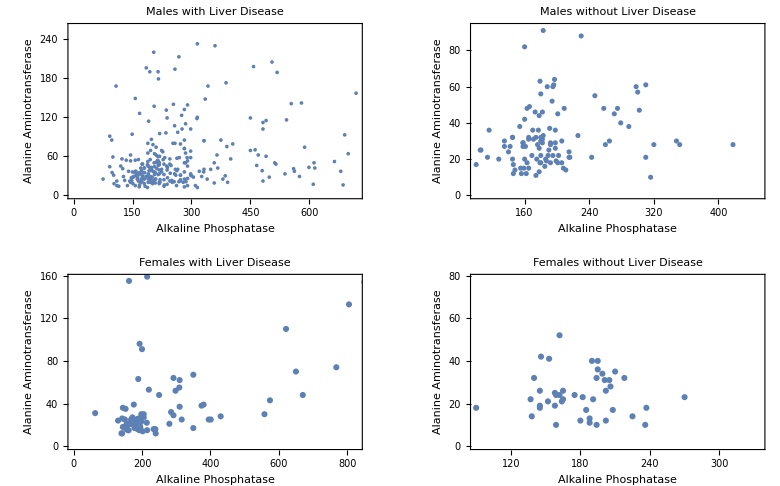

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{5,6}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Alkaline Phosphatase","Alanine Aminotransferase"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{5,6}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Alkaline Phosphatase","Alanine Aminotransferase"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{5,6}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Alkaline Phosphatase","Alanine Aminotransferase"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{5,6}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Alkaline Phosphatase","Alanine Aminotransferase"}]}}]
```

### Correlation Test:

```mathematica
N[Correlation[file[All,"Alkaline_Phosphatase"]//Normal,file[All,"Alanine_Aminotransferase"]//Normal]]
```

0.12568

### Observations:

There is no linear correlation observed between the two variables.

## Relation between Total Proteins and Albumin

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Total Proteins” and “Albumin”.

### Scatter Plot to determine Relationship

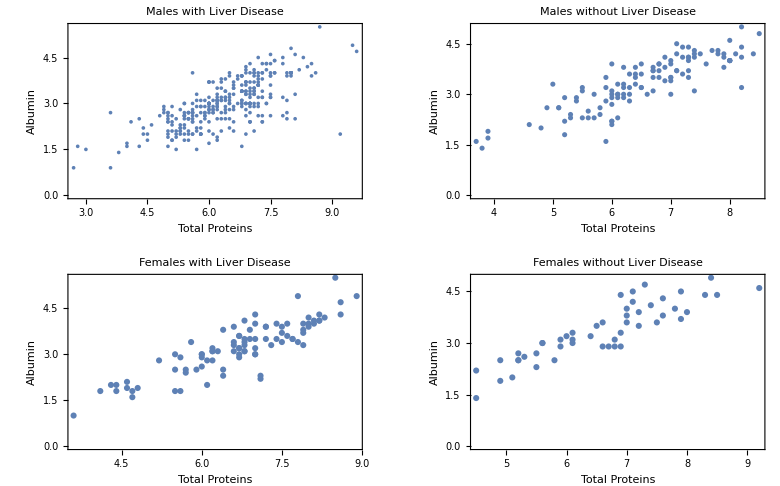

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{8,9}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Total Proteins","Albumin"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{8,9}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Total Proteins","Albumin"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{8,9}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Total Proteins","Albumin"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{8,9}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Total Proteins","Albumin"}]}}]
```

### Correlation Test:

```mathematica
N[Correlation[file[All,"Total_Proteins"]//Normal,file[All,"Albumin"]//Normal]]
```

0.784053

### Observations:

A linear relationship is observed between these two variables with a relatively higher correlation coefficient. There are many types of proteins found in the body apart from albumin and globulin. There is a possibility of removing one of the variables but both the variables will be kept in the model. This is because a decrease in Total Proteins can be due to decrease in amount of the other proteins in body and not always due to decrease in albumin level.

## Relation between Albumin and Albumin and Globulin Ratio

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Albumin” and “A/G Ratio”.

### Scatter Plot to determine Relationship

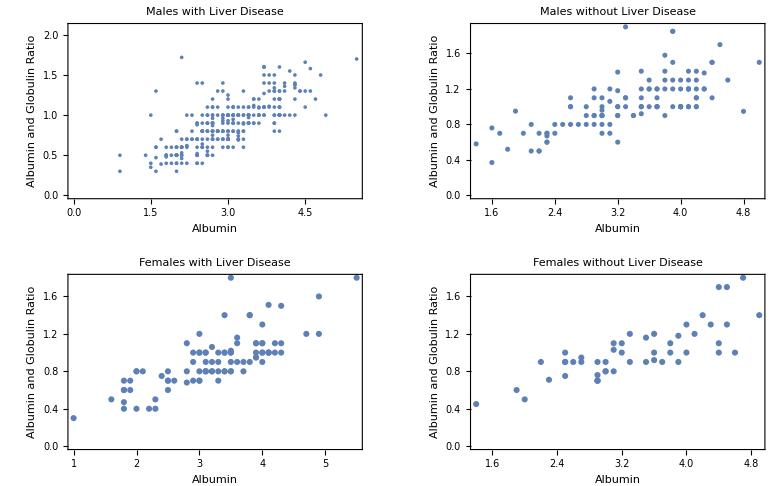

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{9,10}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin","Albumin and Globulin Ratio"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{9,10}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin","Albumin and Globulin Ratio"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{9,10}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin","Albumin and Globulin Ratio"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{9,10}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin","Albumin and Globulin Ratio"}]}}]
```

### Correlation Test:

```mathematica
N[Correlation[file[All,"Albumin"]//Normal,file[All,"Albumin_and_Globulin_Ratio"]//Normal]]
```

0.686321

### Observations:

A linear relationship is observed with a high correlation coefficient. A low A/G ratio may be due to an overproduction of globulin, underproduction of albumin, or loss of albumin making  both the variables important in the model.

## Relation between Total Proteins and Albumin and Globulin Ratio

A scatter plot is plotted and correlation is calculated to view the relationship between the two variables “Total Proteins” and “A/G ratio”.

### Scatter Plot to determine Relationship

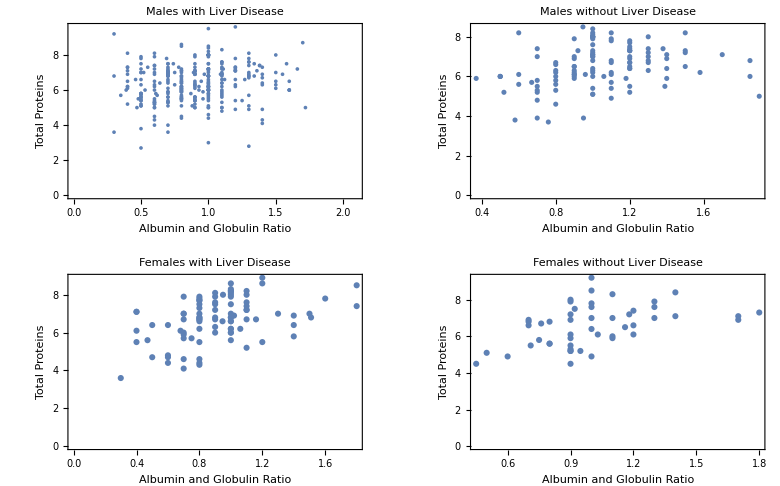

```mathematica
GraphicsGrid[{{ListPlot[Select[newfile,#Gender==0 && #Dataset==1 &][[All,{10,8}]],PlotLabel->Style["Males with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin and Globulin Ratio","Total Proteins"},ImageSize->Medium],
ListPlot[Select[newfile,#Gender==0 && #Dataset==2 &][[All,{10,8}]],PlotLabel->Style["Males without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin and Globulin Ratio","Total Proteins"}]},
{ListPlot[Select[newfile,#Gender==1 && #Dataset==1 &][[All,{10,8}]],PlotLabel->Style["Females with Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin and Globulin Ratio","Total Proteins"}],
ListPlot[Select[newfile,#Gender==1 && #Dataset==2 &][[All,{10,8}]],PlotLabel->Style["Females without Liver Disease",FontSize->16],LabelStyle->Directive[Bold],Frame->True,FrameLabel->{"Albumin and Globulin Ratio","Total Proteins"}]}}]
```

### Correlation Test:

```mathematica
N[Correlation[file[All,"Total_Proteins"]//Normal,file[All,"Albumin_and_Globulin_Ratio"]//Normal]]
```

0.233904

### Observations:

The scatterplot does not indicate any linear relationship and a very low correlation coefficient is obtained.

## Observations:

All the scatter plots and correlation coefficients indicate a  direct relationship between the following features:
Direct Bilirubin & Total Bilirubin
Aspartate Aminotransferase & Alanine Aminotransferase
Total Proteins & Albumin
Albumin_and_Globulin_Ratio & Albumin

Hence we could have omitted a few variables from the model but each test is indicative of different degrees of effect on liver and hence each of the variable is important in classifying a patient as having liver disease or not.

## Machine Learning

In order to apply various classifier algorithms to the dataset, the categorical variable needs to be converted to indicator variables, the dataset needs to be arranged to define the associations and then divided to training and testing dataset. The classifier algorithms need to be trained using the training dataset and then tested using testing dataset. The various models will be compared against various measurements like accuracy, errors, prediction score,confusion matrix, etc. As the data can be classified to two classes (1-> Liver disease, 2-> Not liver disease), linear regression model cannot be used. Linear regression is more suitable for predicting an output that is of continuous value whereas classifier datasets are having outcomes of discrete nature. The regression line is a straight line predicting a real output which can range from negative infinity to positive infinity whereas classifier algorithms predict a probability range between 0 and 1.
The performance measurements against which the models will be compared are:
1) Accuracy
2) Precision
3) F-score
4) Confusion matrix

Handling categorical variable “Gender”

The categorical variable “Gender” is converted to indicator variables (Male and Female). This creates two new columns (Male and Female) where if a patient is male then the column Male has value 1 and the Female column has value as 0. Similarly for a female patient the Female column has 1 and Male column has 0.

```mathematica
Clear[fileprepX,fileprepY,fileprep];
categoryMale[x_]:=If[x=="Male",1,0];
malecol=Map[categoryMale,file[All,"Gender"]]//Normal;
filenew=MapThread[Append,{Normal[file],Thread["Male"->malecol]}]//Dataset;
categoryFemale[x_]:=If[x=="Female",1,0];
femalecol=Map[categoryFemale,file[All,"Gender"]]//Normal;
filenew=MapThread[Append,{Normal[filenew],Thread["Female"->femalecol]}]//Dataset;
fileprepX=filenew[All,{1,3,4,5,6,7,8,9,10,12,13}];
fileprepY=filenew[All,{11}];
fileprep=MapThread[Append,{Normal[fileprepX],Normal[fileprepY]}]//Dataset;
```

Dividing dataset into test and training dataset

The dataset is divided into 2 sets: training and test dataset. A random sampling of the dataset is done and 70% of data is put aside for training dataset and the rest are put into test dataset.

```mathematica
Clear[filetrain,filetest];
SeedRandom[50];
rs=RandomSample[Range[Length[fileprep]]];
train=rs[[1;;Round[Length[fileprep]*0.7]]];
test=rs[[Round[Length[fileprep]*.7]+1;;]];
filetrain=fileprep[[train]]//Dataset;
filetest=fileprep[[test]]//Dataset;
```

Association defined for training and test data

Associations need to be defined for the dataset before it can be applied to classification models. The labelling of dataset that the variables are all input variables except the variable “Dataset” which classifies a patient as having liver disease or not is needed to be done. This association needs to be fed to the models so that it can understand what are the input variables and what output is expected for the inputs given. 
The association defined in this dataset is as below:
{Age,Gender,Total Bilirubin,Direct Bilirubin, Alkaline Phosphatase, Alanine Aminotransferase, Aspartate Aminotransferase, Total Proteins, Albumin. Albumin and Globulin Ratio} --> Dataset
The code “Flatten” helps to flatten out the association defined and lets the dataset know that all the input variables need to be merged together to give the output, i.e. “Dataset”.

The association is defined for both training and test dataset:

```mathematica
trainassoc=filetrain[All,{Most@#->Last@#}&];
trainingdata=Flatten[Normal@trainassoc,1];
testassoc=filetest[All,{Most@#->Last@#}&];
testdata=Flatten[Normal@testassoc,1];
```

Steps of Machine learning

1) The Training dataset is used to train the classifier model by mentioning the method(i.e. algorithm) to be applied.

 	Code: algotraining=Classify[training dataset,Method-><the classifier algorithm>]
 	
 2) A report is generated on the training done
 
 	Code: ClassifierInformation[algotraining]
 	
 3) The test dataset is applied to the training algorithm:
 
 	Code: algotesting = ClassifierMeasurements[algotraining, test dataset]
 	
 4) The measurements against which the standard of the model will be measured are:
 
	a) Accuracy- It gives the proportion of data that has be classified correctly
	b) Recall - It measures the completeness of a classifier. It is calculated as below:
			Recall= (No. of true positive)/(No. of true positives + No. of false negatives)  
	c) Precision- It measures the exactness of the classifier. The precision is calculated as below:
			 Precision= (No. of true positives)/(No. of true positives + No. of true negatives)

	d) F-score - This gives the measure of balance between Precision and Recall. It is calculated as below:
			F-score = 2 (Precision* Recall)/(Precision+Recall)
	e) Error- It gives the proportion of data that has been classified incorrectly. It is calculated as:
			Error =  1- Accuracy
	f) Confusion Matrix - This gives a visual representation of data classified correctly and incorrectly(i.e. the prediction results). The result of Confusion Function is plotted as a matrix in the 	Confusion Matrix.
	
5) Observations are noted down after analysing the model and the classifier measurements.

## Logistic Regression Model

Logistic regression model is a special case of linear regression model where the outcome is categorical (1->Liver Disease, 2-> No liver disease). It predicts the probability of liver disease occurring or not by fitting the data to a logit(sigmoid) function.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
LRtraining=Classify[trainingdata,Method->"LogisticRegression"]
```

ClassifierFunction[…]

2) The ClassifierInformation function generates a report on the properties of the classifier( the algorithm used, accuracy reached, time taken to train the model, etc).

```mathematica
ClassifierInformation[LRtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | LogisticRegression
Accuracy | 66.9 % ± 7.4 %
Loss | 0.617 ± 0.046
Single evaluation time | 5.95 ms/example
Batch evaluation speed | 29.6 examples/ms
Classifier memory | 239. kB
Training examples used | 408 examples
Training time | 4.49 s
 |

3) The trained classifier algorithm is then applied to the test dataset and the results are assessed.

```mathematica
LRtesting=ClassifierMeasurements[LRtraining,testdata]
```

ClassifierMeasurementsObject[…]

```mathematica
LRtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction","Recall"}]//ColumnForm
```

0.731429
<|1→0.838488,2→0.20339|>
0.268571
<|1→0.748466,2→0.5|>
<|1→<|1→122,2→6,Indeterminate→0|>,2→<|1→41,2→6,Indeterminate→0|>|>
<|1→0.953125,2→0.12766|>

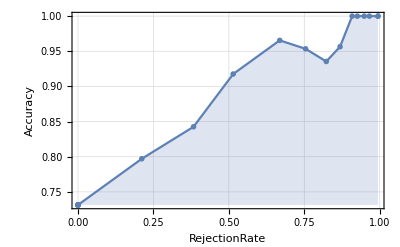

```mathematica
LRtesting["AccuracyRejectionPlot"]
```

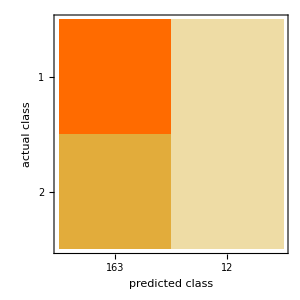

```mathematica
LRtesting["ConfusionMatrixPlot"]
```

### Observations:

1) The Classifier measurements show that 73.15% of the data is classified correctly and 26.8% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 122 data correctly predicted to be belonging to Dataset=1 and 6 data belonging to Dataset =1 has been incorrectly classified to be belonging to Dataset =2
	b) 6  data correctly predicted to be belonging to Dataset=2 and 41 data belonging to Dataset =2 has been incorrectly classified to be belonging to Dataset =1
3) F-score of Dataset=1 is calculated as 0.838 and Dataset=2 is 0.20.

## Gaussian Naive Bayes Classifier

Bayes’ Theorem finds the probability of an event occurring given the probability of another event that has already occurred.
The Gaussian Naive Bayes Classifier is a collection of classification algorithms based on Bayes’ Theorem. The principle of this algorithm is that every pair of feature being classified is independent of each other.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
GNBtraining=Classify[trainingdata,Method->"NaiveBayes"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[GNBtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | NaiveBayes
Accuracy | 64.5 % ± 7.5 %
Loss | 1.16 ± 0.43
Single evaluation time | 7. ms/example
Batch evaluation speed | 11.2 examples/ms
Classifier memory | 225. kB
Training examples used | 408 examples
Training time | 2.25 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
GNBtesting=ClassifierMeasurements[GNBtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
GNBtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.72
<|1→0.804781,2→0.505051|>
0.28
<|1→0.821138,2→0.480769|>
<|1→<|1→101,2→27,Indeterminate→0|>,2→<|1→22,2→25,Indeterminate→0|>|>

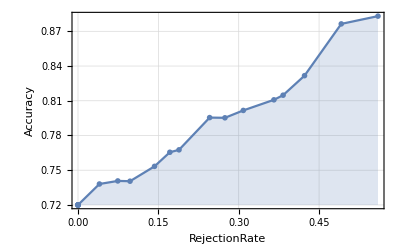

```mathematica
GNBtesting["AccuracyRejectionPlot"]
```

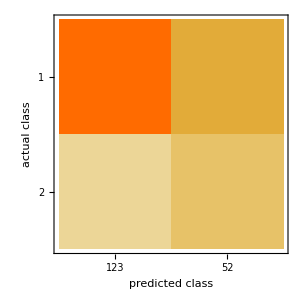

```mathematica
GNBtesting["ConfusionMatrixPlot"]
```

### Observations:

1) The Classifier measurements show that 72% of the data is classified correctly and 28% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 101 data correctly predicted to be belonging to Dataset=1 and 27 data belonging to Dataset =1 has been incorrectly classified to be belonging to Dataset =2
	b) 25  data correctly predicted to be belonging to Dataset=2 and 22 data belonging to Dataset =2 has been incorrectly classified to be belonging to Dataset =1
3) F-score of Dataset=1 is calculated as 0.80 and Dataset=2 is 0.50.

## Decision Tree

This classifier algorithm uses a decision tree to go from an observation to the conclusion about the item’s target value. 
A Decision Tree consists of :
		a) Nodes : Test for the value of a certain attribute.
		b) Edges/ Branch : Correspond to the outcome of a test and connect to the next node or leaf.
		c) Leaf nodes : Terminal nodes that predict the outcome (represent class labels or class distribution).
There are two main types of Decision Trees:
		a) Classification Trees.
		b) Regression Trees.
In this case the Classification trees will be used as the output is not continuous but discrete in nature (1 or 2).

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
DTtraining=Classify[trainingdata,Method->"DecisionTree"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[DTtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | DecisionTree
Accuracy | 66.8 % ± 1.8 %
Loss | 0.675 ± 0.023
Single evaluation time | 6.03 ms/example
Batch evaluation speed | 28.3 examples/ms
Classifier memory | 171. kB
Training examples used | 408 examples
Training time | 1.96 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
DTtesting=ClassifierMeasurements[DTtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
DTtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.731429
<|1→0.825279,2→0.419753|>
0.268571
<|1→0.787234,2→0.5|>
<|1→<|1→111,2→17,Indeterminate→0|>,2→<|1→30,2→17,Indeterminate→0|>|>

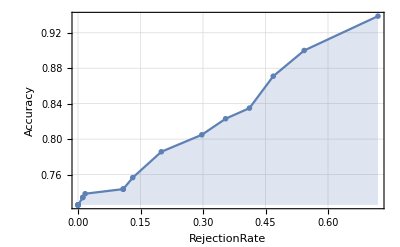

```mathematica
DTtesting["AccuracyRejectionPlot"]
```

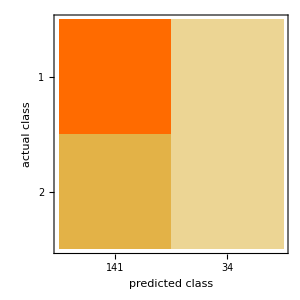

```mathematica
DTtesting["ConfusionMatrixPlot"]
```

### Observations:

1) The Classifier measurements show that 73.1% of the data is classified correctly and 26.9% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 111 data correctly predicted to be belonging to Dataset=1 and 17 data belonging to Dataset =1 has been incorrectly classified to be belonging to Dataset =2
	b) 17  data correctly predicted to be belonging to Dataset=2 and 30 data belonging to Dataset =2 has been incorrectly classified to be belonging to Dataset =1
3) F-score of Dataset=1 is calculated as 0.825 and Dataset=2 is 0.419.

## Nearest Neighbours Algorithm

The nearest neighbour algorithm stores all the available cases and classifies the new data based on a similarity measure. It is used to classify a data based on how its neighbours are classified. Similarity is defined using the Euclidean distance method between two data points.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
NNtraining=Classify[trainingdata,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[NNtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | NearestNeighbors
Accuracy | 69. % ± 3.1 %
Loss | 0.575 ± 0.035
Single evaluation time | 6.39 ms/example
Batch evaluation speed | 14.6 examples/ms
Classifier memory | 213. kB
Training examples used | 408 examples
Training time | 2.41 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
NNtesting=ClassifierMeasurements[NNtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
NNtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.731429
<|1→0.844884,2→0.|>
0.268571
<|1→0.731429,2→Indeterminate|>
<|1→<|1→128,2→0,Indeterminate→0|>,2→<|1→47,2→0,Indeterminate→0|>|>

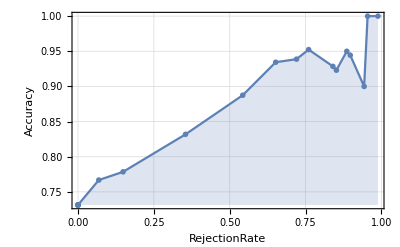

```mathematica
NNtesting["AccuracyRejectionPlot"]
```

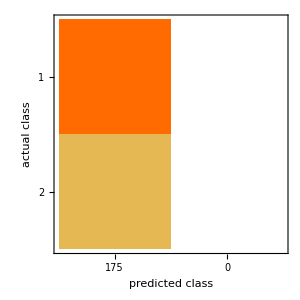

```mathematica
NNtesting["ConfusionMatrixPlot"]
```

### Observations

1) The Classifier measurements show that 73.1% of the data is classified correctly and 26.3% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 128 data correctly predicted to be belonging to Dataset=1 
	b) 47  data incorrectly predicted to be belonging to Dataset=2 
No data has been wrongly classified.
3) F-score of Dataset=1 is calculated as 0.844 and Dataset=2 is 0 as none of the data belonging to “2” has been identified.

## Artificial Neural Network algorithm

Artificial neural networks (ANN) are computing systems that are inspired by, but not identical to, biological neural networks that constitute animal brains. Such systems “learn” to perform tasks by considering examples, generally without being programmed with task-specific rules.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
ANNtraining=Classify[trainingdata,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[ANNtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | NeuralNetwork
Accuracy | 68.1 % ± 7.3 %
Loss | 0.613 ± 0.061
Single evaluation time | 7.28 ms/example
Batch evaluation speed | 18.5 examples/ms
Classifier memory | 1.26 MB
Training examples used | 408 examples
Training time | 22.1 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
ANNtesting=ClassifierMeasurements[ANNtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
ANNtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.731429
<|1→0.825279,2→0.419753|>
0.268571
<|1→0.787234,2→0.5|>
<|1→<|1→111,2→17,Indeterminate→0|>,2→<|1→30,2→17,Indeterminate→0|>|>

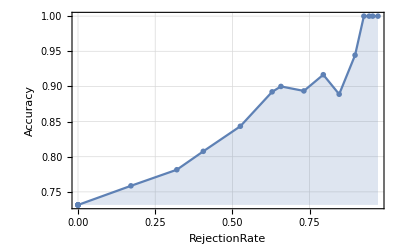

```mathematica
ANNtesting["AccuracyRejectionPlot"]
```

```mathematica
ANNtesting["ConfusionMatrixPlot"]
```

-Graphics-

### Observations:

1) The Classifier measurements show that 73.14% of the data is classified correctly and 26.8% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 111 data correctly predicted to be belonging to Dataset=1 and 17 data belonging to Dataset =1 has been incorrectly classified to be belonging to Dataset =2
	b) 17  data correctly predicted to be belonging to Dataset=2 and 30 data belonging to Dataset =2 has been incorrectly classified to be belonging to Dataset =1
3) F-score of Dataset=1 is calculated as 0.825 and Dataset=2 is 0.419.

## Support Vector Machine Algorithm

“Support Vector Machine” (SVM) is a supervised machine learning algorithm used mainly in classification problems. In this algorithm, each data item is plotted as a point in n-dimensional space (where n is number of features the data point has) with the value of each feature being the value of a particular coordinate. Then, the classification is performed by finding the hyper-plane that differentiate the two classes very well.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
SVMtraining=Classify[trainingdata,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[SVMtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | SupportVectorMachine
Accuracy | 72.5 % ± 3.4 %
Loss | 0.581 ± 0.038
Single evaluation time | 8.79 ms/example
Batch evaluation speed | 14.6 examples/ms
Classifier memory | 312. kB
Training examples used | 408 examples
Training time | 5.92 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
SVMtesting=ClassifierMeasurements[SVMtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
SVMtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.731429
<|1→0.844884,2→0.|>
0.268571
<|1→0.731429,2→Indeterminate|>
<|1→<|1→128,2→0,Indeterminate→0|>,2→<|1→47,2→0,Indeterminate→0|>|>

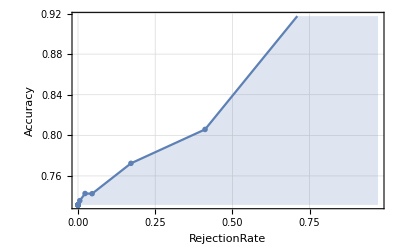

```mathematica
SVMtesting["AccuracyRejectionPlot"]
```

```mathematica
SVMtesting["ConfusionMatrixPlot"]
```

-Graphics-

### Observations:

1) The Classifier measurements show that 73.2% of the data is classified correctly and 26.8% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) All of 128 data correctly predicted to be belonging to Dataset=1 
	b) All of 47  data are incorrectly predicted to be belonging to Dataset=1. The output with Dataset as “2” has not been identified in any of the cases.
3) F-score of Dataset=1 is calculated as 0.844 and Dataset=2 is 0 because this class has not been identified.

## Random Forest Algorithm

An ensemble method or ensemble learning algorithm consists of aggregating multiple outputs made by a diverse set of predictors to obtain better results. Formally, based on a set of “weak” learners, a “strong” learner for a model is used. Therefore, the purpose of using ensemble methods is: to average out the outcome of individual predictions by diversifying the set of predictors, thus lowering the variance, to arrive at a powerful prediction model that reduces over-fitting of the training dataset.
A Random Forest (strong learner) is built as an ensemble of Decision Trees (weak learners) to perform different tasks such as classification.

1) The training dataset is fed into the classifier algorithm to train the model.

```mathematica
RFtraining=Classify[trainingdata,Method->"RandomForest"]
```

ClassifierFunction[…]

2) The report of the training is generated:

```mathematica
ClassifierInformation[RFtraining]
```

Classifier information
Input type | Mixed (number: 11)
Classes | ,,12
Method | RandomForest
Accuracy | 70.9 % ± 2.4 %
Loss | 0.584 ± 0.012
Single evaluation time | 13.6 ms/example
Batch evaluation speed | 7.4 examples/ms
Classifier memory | 276. kB
Training examples used | 408 examples
Training time | 2.33 s
 |

3) The test dataset is applied to the trained model to classify the data to the two classes.

```mathematica
RFtesting=ClassifierMeasurements[RFtraining,testdata]
```

ClassifierMeasurementsObject[…]

4) The testing measurements are obtained:

```mathematica
RFtesting[{"Accuracy","FScore","Error",  "Precision","ConfusionFunction"}]//ColumnForm
```

0.76
<|1→0.854167,2→0.322581|>
0.24
<|1→0.76875,2→0.666667|>
<|1→<|1→123,2→5,Indeterminate→0|>,2→<|1→37,2→10,Indeterminate→0|>|>

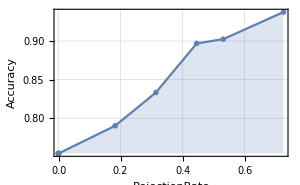

```mathematica
RFtesting["AccuracyRejectionPlot"]
```

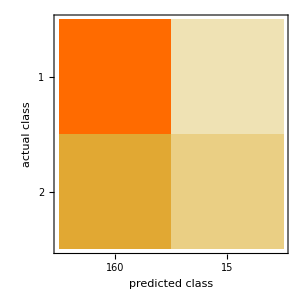

```mathematica
RFtesting["ConfusionMatrixPlot"]
```

### Observations:

1) The Classifier measurements show that 76% of the data is classified correctly and 24% data is classified incorrectly. 
2) The Confusion matrix shows : 
	a) 123 data correctly predicted to be belonging to Dataset=1 and 5 data belonging to Dataset =1 has been incorrectly classified to be belonging to Dataset =2
	b) 10  data correctly predicted to be belonging to Dataset=2 and 37 data belonging to Dataset =2 has been incorrectly classified to be belonging to Dataset =1
3) F-score of Dataset=1 is calculated as 0.85 and Dataset=2 is 0.32.

Conclusion

The Gaussian Naive Bayes algorithm had the lowest accuracy level and so incorrectly classified 49 cases. The Support Vector Machine Algorithm and Nearest Neighbour algorithm had around 73% accuracy but both of them failed to identify any data belonging to Class “2” and so all were identified to be belonging to Class “1”. All the models had almost same accuracy but the Random Forest algorithm had the highest accuracy rate of 76% and correctly identified most of the cases(133 out of 175). The training dataset needs to be of bigger size and properly created by adding different cases for all the 10 variables so that the model can be trained to understand significance of each variable and hence classify correctly.

## Bibliography:

https://www.healthline.com/health/liver-function-tests#types

https://www.guidelinesinpractice.co.uk/liver-disease/liver-blood-tests-how-to-interpret-abnormal-results/453912.article

https://timesofindia.indiatimes.com/life-style/health-fitness/health-news/is-liver-disease-the-next-major-lifestyle-disease-of-india-after-diabetes-and-bp/articleshow/58122706.cms

https://machinelearningmastery.com/classification-accuracy-is-not-enough-more-performance-measures-you-can-use/

https://www.geeksforgeeks.org/naive-bayes-classifiers/

https://towardsdatascience.com/decision-tree-classification-de64fc4d5aac

https://en.wikipedia.org/wiki/Decision_tree_learning

https://towardsdatascience.com/a-simple-introduction-to-k-nearest-neighbors-algorithm-b3519ed98e

https://towardsdatascience.com/neural-network-algorithms-learn-how-to-train-ann-736dab9e6299

https://www.analyticsvidhya.com/blog/2017/09/understaing-support-vector-machine-example-code/